```mathematica
(*Solución analítica*)
DSolve[{y''[x]+4*y[x]==Sin[x],y[0]==0,y'[0]==1},y,{x,0,1}]
```

{{y→Function[{x},1/3 (Sin[x]+Sin[2 x])]}}

```mathematica
s[x_]:=1/3*(Sin[x]+Sin[2*x]);
(*datos usuario: y'=u*)
y0=0;
u0=1;
f[x_,y_,u_]:={u,Sin[x]-4*y};
a=0;
b=1;
h=0.01;
niter=IntegerPart[(b-a)/h];
sol={{a,y0}};
error={{a,Abs[y0-s[a]]}};
(*Programa*)
x0=a;
For[i=1,i≤niter,i++,
{y0,u0}={y0,u0}+h*f[x0,y0,u0];
x0=x0+h;
sol=AppendTo[sol,{x0,y0}];
error=AppendTo[error,{x0,Abs[y0-s[x0]]}];
];
```

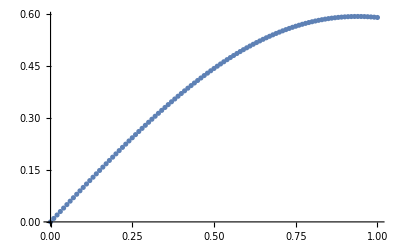

```mathematica
g1=ListPlot[sol]
```

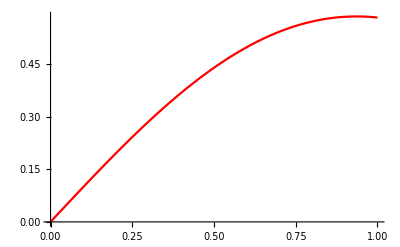

```mathematica
g2=Plot[s[x],{x,0,1},PlotStyle->Red]
```

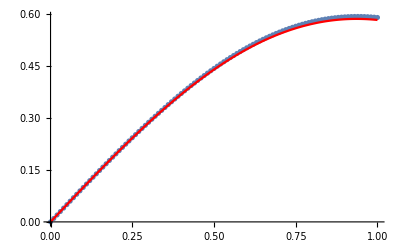

```mathematica
Show[g1,g2]
```